```mathematica
(*Define the d in the median for GES and SGES use*)
```

```mathematica
dtildeFisher=Function[k, Exp[2*k]*(6*Sqrt[k]-(3+8*k)DawsonF[2*Sqrt[k]])/(24*Pi*Sqrt[2]*k^(1.5)*(BesselI[0,2*k]-BesselI[1,2*k]))]
```

Function[k,(Exp[2 k] (6 √k-(3+8 k) DawsonF[2 √k]))/(24 π √2 k^1.5 (BesselI[0,2 k]-BesselI[1,2 k]))]

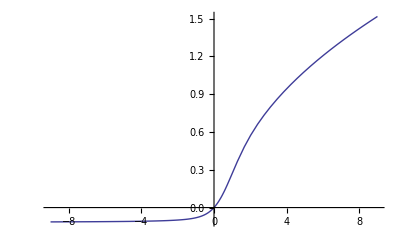

```mathematica
Plot[Function[k,(Exp[2 k] (6 √k-(3+8 k) DawsonF[2 √k]))/(24 π √2 k^1.5 (BesselI[0,2 k]-BesselI[1,2 k]))][x],{x,-9.,9.}]
```

```mathematica
(*Find GES of median for Fisher family*)
```

```mathematica
Limit[1/(Sqrt[2]*dtildeFisher[k]),k->0]
```

∞

```mathematica
Limit[1/(Sqrt[2]*dtildeFisher[k]),k->Infinity]
```

0.

```mathematica
(*Define d for the mean in Fisher Family*)
dhatFisher=Function[k,((k+1)*BesselI[1,2k]-k*BesselI[0,2k])/(3*k*(BesselI[0,2k]-BesselI[1,2k]))]
```

Function[k,((k+1) BesselI[1,2 k]-k BesselI[0,2 k])/(3 k (BesselI[0,2 k]-BesselI[1,2 k]))]

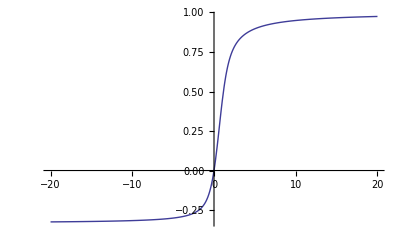

```mathematica
Plot[Function[k,((k+1) BesselI[1,2 k]-k BesselI[0,2 k])/(3 k (BesselI[0,2 k]-BesselI[1,2 k]))][x],{x,-20.,20.}]
```

```mathematica
(*GES for the mean and Fisher distribution*)
Limit[1/dhatFisher[k],k->0]
```

∞

```mathematica
Limit[1/dhatFisher[k],k->Infinity]
```

1

```mathematica
(*Fisher information matrix for matrix Fisher distribution*)
FIFisher=Function[k,(2)*((k+1)*BesselI[1,2k]-k*BesselI[0,2k])/(3*(BesselI[0,2k]-BesselI[1,2k]))]
```

Function[k,(2 ((k+1) BesselI[1,2 k]-k BesselI[0,2 k]))/(3 (BesselI[0,2 k]-BesselI[1,2 k]))]

```mathematica
(*SGES of the median for the Fisher family*)
```

```mathematica
Limit[Sqrt[FIFisher[k]]/(dtildeFisher[k]*Sqrt[2]),k->0]
```

3.60717

```mathematica
Limit[Sqrt[FIFisher[k]]/(dtildeFisher[k]*Sqrt[2]),k->Infinity]
```

4.71239

```mathematica
(*SGES for the mean for the Fisher Family*)
Limit[Sqrt[FIFisher[k]]/dhatFisher[k],k->0]
```

√6

```mathematica
Limit[Sqrt[FIFisher[k]]/dhatFisher[k],k->Infinity]
```

∞

```mathematica
(*Do the Same thing for the Cayley Distribution*)
```

```mathematica
dtildeCayley=Function[k,k*Sqrt[2]*Gamma[k+2]/(3*Sqrt[Pi]*Gamma[k+2.5])]
```

Function[k,(k √2 Gamma[k+2])/(3 √π Gamma[k+2.5])]

```mathematica
(*Median GES for the Cayley Family)
```

```mathematica
Limit[1/(Sqrt[2]*dtildeCayley[k]),k->0]
```

∞

```mathematica
Limit[1/(Sqrt[2]*dtildeCayley[k]),k->Infinity]
```

0.

```mathematica
(*Mean GES for the Cayley Family*)
```

```mathematica
dhatCayley=Function[k,k/(k+2)]
```

Function[k,k/(k+2)]

```mathematica
Limit[1/dhatCayley[k],k->0]
```

∞

```mathematica
Limit[1/dhatCayley[k],k->Infinity]
```

1

```mathematica
(*Fisher Information matrix for Cayley Family*)
```

```mathematica
FICayley=Function[k,k^2/(2k-1)]
```

Function[k,k^2/(2 k-1)]

```mathematica
(*Median SGES for the Cayley family*)
```

```mathematica
Limit[Sqrt[FICayley[k]]/(dtildeCayley[k]*Sqrt[2]),k->0.5]
```

∞

```mathematica
Limit[Sqrt[FICayley[k]]/(dtildeCayley[k]*Sqrt[2]),k->Infinity]
```

1.87997

```mathematica
(*Mean SGES for the Cayley Family*)
```

```mathematica
Limit[Sqrt[FICayley[k]]/dhatCayley[k],k->0.5]
```

∞

```mathematica
Limit[Sqrt[FICayley[k]]/dhatCayley[k],k->Infinity]
```

∞

```mathematica
(*Self-standardized sensitivity for median for Cayley Family*)
ctildeCayley=Function[k,(2*k+1)/(6*(k+2))]
```

Function[k,(2 k+1)/(6 (k+2))]

```mathematica
Limit[Sqrt[1/ctildeCayley[k]],k->0]
```

2 √3

```mathematica
Limit[Sqrt[1/ctildeCayley[k]],k->Infinity]
```

√3

```mathematica
(*Self-standardized sensitivity for median for Fisher Family*)
ctildeFisher=Function[k,BesselI[1,2k]/(12*k*(BesselI[0,2k]-BesselI[1,2k]))]
```

Function[k,BesselI[1,2 k]/(12 k (BesselI[0,2 k]-BesselI[1,2 k]))]

```mathematica
Limit[Sqrt[1/ctildeFisher[k]],k->0]
```

2 √3

```mathematica
Limit[Sqrt[1/ctildeFisher[k]],k->Infinity]
```

√3

```mathematica
(*Self-standardized sensitivity for the mean in the Fisher family*)
```

```mathematica
chatFisher=Function[k,((k+1)*BesselI[1,2k]-k*BesselI[0,2k])/(3*k^2*(BesselI[0,2k]-BesselI[1,2k]))]
```

Function[k,((k+1) BesselI[1,2 k]-k BesselI[0,2 k])/(3 k^2 (BesselI[0,2 k]-BesselI[1,2 k]))]

```mathematica
Limit[Sqrt[2/chatFisher[k]],k->0]
```

√6

```mathematica
Limit[Sqrt[2/chatFisher[k]],k->Infinity]
```

∞

```mathematica
(*Last ditch effort, define SGES of median for Cayley by using AV of moment estimator instead of Fisher Information*)
chatCayley=Function[k,(4*k+2)/(k^2+5k+6)]
```

Function[k,(4 k+2)/(k^2+5 k+6)]

```mathematica
Limit[dhatCayley[k]/(dtildeCayley[k]*Sqrt[chatCayley[k]]),k->0]
```

4.32861

```mathematica
Limit[dhatCayley[k]/(dtildeCayley[k]*Sqrt[chatCayley[k]]),k->Infinity]
```

1.87997